# Critical congestion

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Flows"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U7},{8,U8},{9,U9}},"Switching Costs"->{}|>;
```

ligar o 6 com o 9 esta dando um sistema sem solucao ... ..(parece que nao...)

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{
{0,1,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,1,1,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,1,0,0},
{0,0,0,0,0,0,0,1,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Flows"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U7},{8,U8},{9,U9}},"Switching Costs"->{}|>;
```

6 com 8

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{
{0,1,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,1,1,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,1,0,0},
{0,0,0,0,0,0,0,1,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Flows"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U7},{8,U8},{9,U9}},"Switching Costs"->{}|>;
```

4 com 8?

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{
{0,1,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,1,1,0,0,0,0},
{0,0,0,0,0,1,0,1,0},
{0,0,0,0,0,1,1,0,0},
{0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Flows"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U7},{8,U8},{9,U9}},"Switching Costs"->{}|>;
```

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{
{0,1,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,1,1,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,1,0,0},
{0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Flows"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U7},{8,U8},{9,U9}},"Switching Costs"->{}|>;
```

```mathematica
d2e1 = Data2Equations[Data/.{I1->100,I2->200,U7->5,U8->50, U9->0}];
```

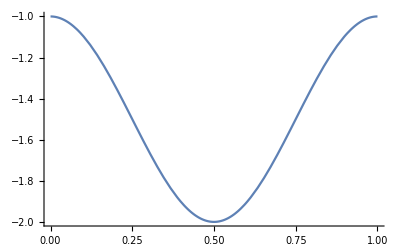
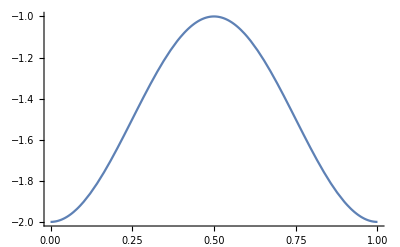
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

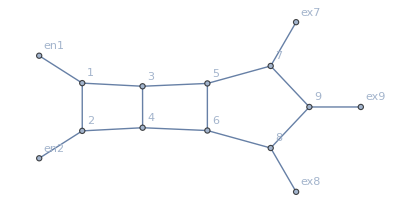

Switching costs simplified in 0.040727 seconds.

Balance equations solved in 0.006357 seconds.

TripleClean took 0.014737 seconds.

TripleClean again (with some more equalities) took 0.017082 seconds.

```mathematica
V[x_,edge_]:=Which[
edge===1->2||edge===3->4||edge===5->6||edge===7->9||edge===8->9,
Sin[ Pi (x+1/2)]^2-2,
edge===6->8||edge===5->7,
Sin[ 1/2Pi (x)]-2,
edge===en1->1||edge===en2->2,
0,
edge===8->ex8||edge===9->ex9,
0,
True,
Sin[Pi (x)]^2-2]/.DirectedEdge->List;
Plot[V[x,#],{x,0,1}]&/@(DirectedEdge@@@d2e["edgeList"])
d2e = MFGPreprocessing[d2e1];
```

```mathematica
(nn=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

MFGSS: Calculated the cost plus currents for the flow in 0.000305 seconds.

MFGS: Selecting inequalities by transition flow took 0.010207 seconds.

MFGSS: Simplifying inequalities by transition flow took 0.168427 seconds.

Final: RemoveDuplicates took 0.001072 seconds

Final: Iterative DNF convertion took 0.138807 seconds to terminate.

Final: Reducing (each alternative) took 0.000781 seconds to terminate.

MFGSS: System is True

{0.640026,Null}

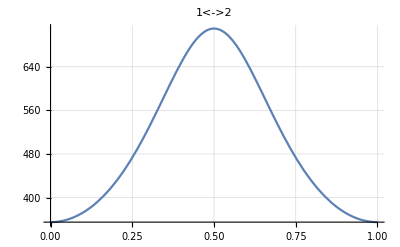
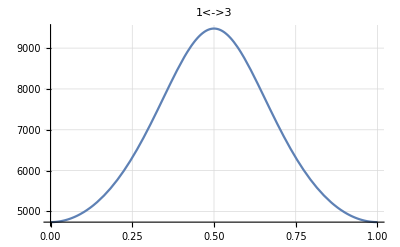
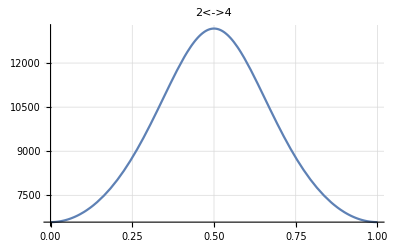
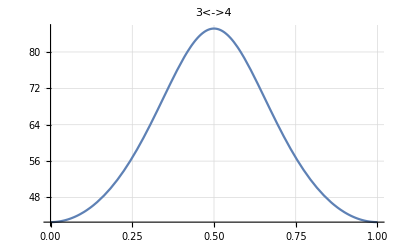
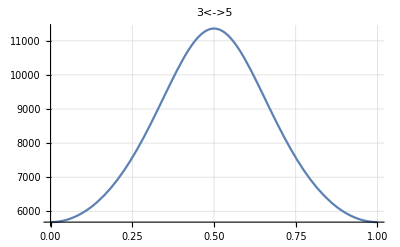
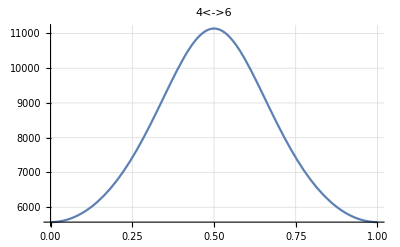
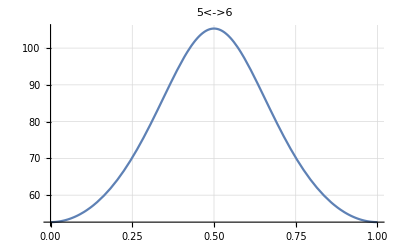
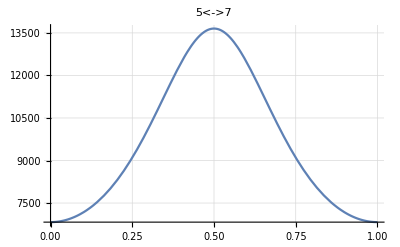

```mathematica
plotM[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
plotU[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
```

# Non-linear problems

```mathematica
{bb,mm,cc,vv}=GetKirchhoffMatrix[nn];
```

```mathematica
alpha[x_]:=.1
```

```mathematica
IntM[-j1+j2,1->2]
```

IntM[-j1+j2,1->2]

```mathematica
IntM[3,1->2]
```

1.79436

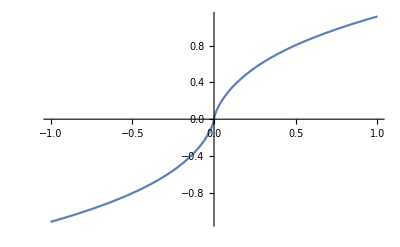

```mathematica
Plot[IntM[x,1->2],{x,-1,1}]
```

```mathematica
cc[vv]
```

{j1 j2+Abs[IntM[-j1+j2,1->2]],j1 j2+Abs[IntM[-j1+j2,1->2]],j3 j4+Abs[IntM[-j3+j4,1->3]],j3 j4+Abs[IntM[-j3+j4,1->3]],j5 j6+Abs[IntM[-j5+j6,2->4]],j5 j6+Abs[IntM[-j5+j6,2->4]],j7 j8+Abs[IntM[-j7+j8,3->4]],j7 j8+Abs[IntM[-j7+j8,3->4]],j10 j9+Abs[IntM[j10-j9,3->5]],j10 j9+Abs[IntM[j10-j9,3->5]],j11 j12+Abs[IntM[-j11+j12,4->6]],j11 j12+Abs[IntM[-j11+j12,4->6]],j13 j14+Abs[IntM[-j13+j14,5->6]],j13 j14+Abs[IntM[-j13+j14,5->6]],j15 j16+Abs[IntM[-j15+j16,5->7]],j15 j16+Abs[IntM[-j15+j16,5->7]],j17 j18+Abs[IntM[-j17+j18,6->8]],j17 j18+Abs[IntM[-j17+j18,6->8]],j19 j20+Abs[IntM[-j19+j20,7->9]],j19 j20+Abs[IntM[-j19+j20,7->9]],0,j23 j24+Abs[IntM[-j23+j24,8->9]],j23 j24+Abs[IntM[-j23+j24,8->9]],0,0,0,0,jt1 jt3,1000000+jt2 jt5,jt1 jt3,1000000+jt4 jt6,jt2 jt5,jt4 jt6,jt7 jt9,1000000+jt11 jt8,jt7 jt9,1000000+jt10 jt12,jt11 jt8,jt10 jt12,jt13 jt15,jt14 jt17,jt13 jt15,jt16 jt18,jt14 jt17,jt16 jt18,jt19 jt21,jt20 jt23,jt19 jt21,jt22 jt24,jt20 jt23,jt22 jt24,jt25 jt27,jt26 jt29,jt25 jt27,jt28 jt30,jt26 jt29,jt28 jt30,jt31 jt33,jt32 jt35,jt31 jt33,jt34 jt36,jt32 jt35,jt34 jt36,jt37 jt39,jt38 jt41,jt37 jt39,jt40 jt42,1000000+jt38 jt41,1000000+jt40 jt42,jt43 jt45,jt44 jt47,jt43 jt45,jt46 jt48,1000000+jt44 jt47,1000000+jt46 jt48,jt49 jt51,jt50 jt53,jt49 jt51,jt52 jt54,1000000+jt50 jt53,1000000+jt52 jt54}

1

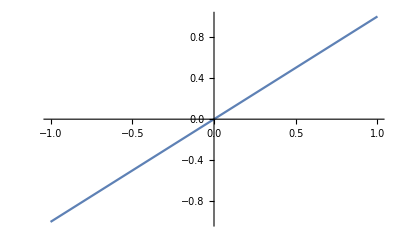

```mathematica
alpha[a]
```

```mathematica
alpha[x_]:=.1;
nn=NonLinear[nn];//AbsoluteTiming
```

{220.996,Null}

```mathematica
alpha[x_]:=.2;
nn=NonLinear[nn];//AbsoluteTiming
```

{225.56,Null}

```mathematica
alpha[x_]:=.2;
nn=NonLinear[nn];//AbsoluteTiming
```

{227.287,Null}

```mathematica
IsNonLinearSolution[nn];
```

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
d2e=D2E[Data/.{I1-> 130,I2->(*129*)(*20*)2, U1-> 20,U2->100,U3->0}];
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 130,I2->(*129*)(*20*)129, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming(*does not get all us in the first "step"*)
```

{2.10546,<|u1→18356/41,u2→18421/41,u3→18356/41,u4→12961/41,u5→18421/41,u6→13197/41,u7→12961/41,u8→13197/41,u9→12961/41,u10→7330/41,u11→13197/41,u12→8209/41,u13→7330/41,u14→8209/41,u15→7330/41,u16→20,u17→8209/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→18356/41,u30→18356/41,u31→18421/41,u32→18421/41,j1→65/41,j2→0,j3→0,j4→5395/41,j5→0,j6→5224/41,j7→236/41,j8→0,j9→0,j10→5631/41,j11→0,j12→4988/41,j13→879/41,j14→0,j15→0,j16→6510/41,j17→0,j18→4109/41,j19→0,j20→20,j21→0,j22→5690/41,j23→0,j24→100,j25→0,j26→9/41,j27→0,j28→120,j29→0,j30→130,j31→0,j32→129|>}

### Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1-> 130,I2->(*129*)(*20*)129, U1-> 20,U2->100,U3->0}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0.2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,1]//AbsoluteTiming
```

```mathematica
jsys=(d2e["EqCriticalCase"]/. uvalues)&&d2e["EqPosJs"]&&d2e["EqCurrentCompCon"];FFR
```

```mathematica
d2e
```

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
getVar::usage ="getVar[exp] returns the variables in exp"
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

### got to fix the “got And”!!

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
us/.(Expand/@rules)
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

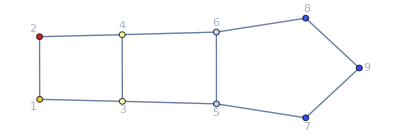

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rule]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

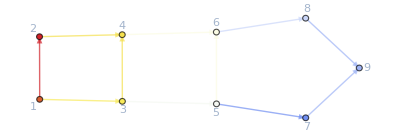

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

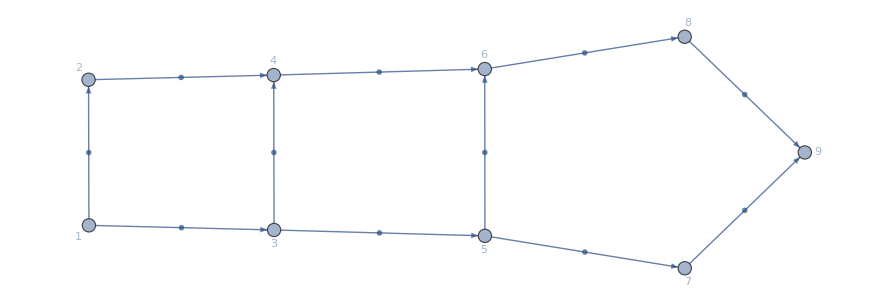

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

systemgrid

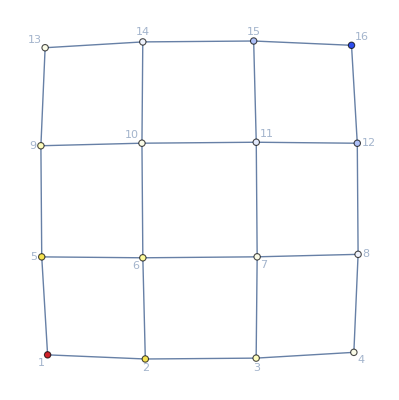

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,180,10}]
```

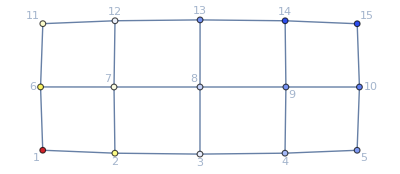

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

# TestZone

#### This is the winning code! Try this on CriticalCongestionSolverNewReduce

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

## New Example

```mathematica
eme=3;
ege=3;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@Data2Equations[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,rulesgrid}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
rulesgrid = rulesgrid["AssoCritical"];
```

Iterative DNF convertion took 42.7454 seconds to terminate

Iterative DNF convertion took 0.919492 seconds to terminate

Iterative DNF convertion took 0.242593 seconds to terminate

Iterative DNF convertion took 0.057489 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 0≤jt22≤1

Picked one value for the variable(s) {jt22} {1/2} (respectively)

45.7742

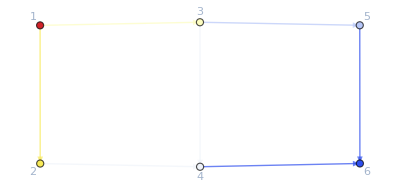

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```